ClearAll

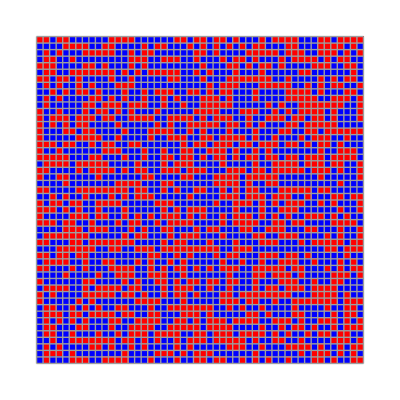

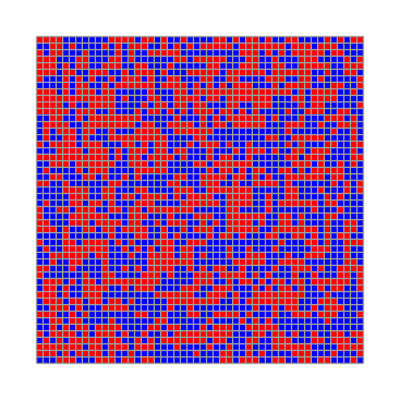

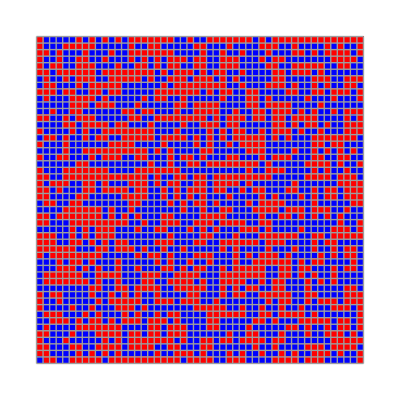

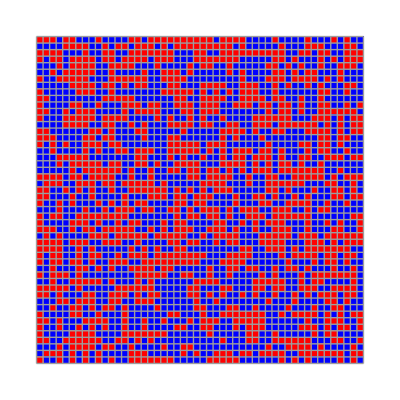

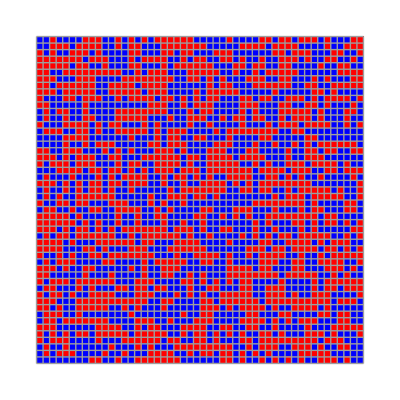

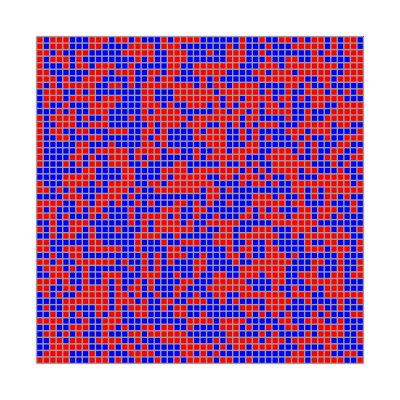

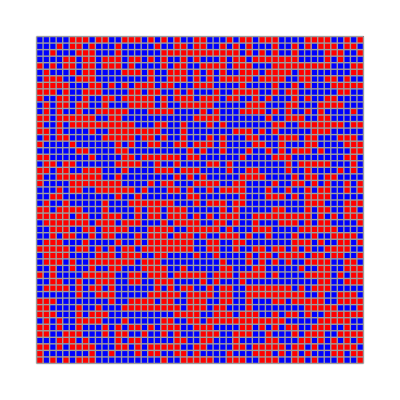

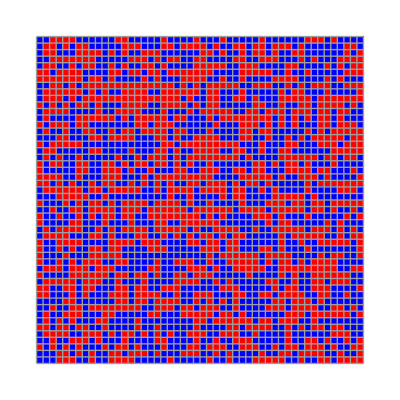

-Graphics-

```mathematica
ClearAll
Clear[s,i,j]
nn=50;
TT=10;
ediff=0;
maxN=10^5;

initialize:=(
s=RandomChoice[{-1,1},{nn,nn}];
)

deltau[i_,j_]:=(
t=b=l=r=0;
If[   i==1,t=s[[nn]][[j]],t=s[[i-1]][[j]]     ];
If[   i==nn,b=s[[1]][[j]],b=s[[i+1]][[j]]     ];
If[   j==1,l=s[[i]][[nn]],l=s[[i]][[j-1]]     ];
If[   j==nn,r=s[[i]][[1]],r=s[[i]][[j+1]]     ];
ediff=(2×(s[[i]][[j]])×(t+r+b+l));
(*Print[t,r,b,l];*)
)

initialize
s;
stores=Table[0,{k,1,maxN}];
ArrayPlot[s,ColorRules->{1->Blue,-1->Red},Mesh->True]
For[cnt=1,cnt≤maxN,cnt++,
i=RandomInteger[{1,nn}];
j=RandomInteger[{1,nn}];
deltau[i,j];
If[   ediff<0,s[[i]][[j]]=-s[[i]][[j]],
If[(RandomReal[]<ⅇ^(-ediff/TT)),s[[i]][[j]]=-s[[i]][[j]]]
];
If[Mod[cnt,10000]==0,Print[ArrayPlot[s,ColorRules->{1->Blue,-1->Red},Mesh->True]];
];
];
ArrayPlot[s,ColorRules->{1->Blue,-1->Red},Mesh->True]
```